## Visualizing Miller’s “Probability of Replication”

Here is Miller’s formula for p_ra.

```mathematica
Subscript[p, ra][α_,β_,γ_]:=(γ (1-β)^2+1/2 (1-γ) α^2)/(γ (1-β)+(1-γ) α);
```

Here is a function which calculates (and visualizes) the region of {β,γ} parameter space in which p_ra > t — for a given significance level α, and probability threshold t.

```mathematica
ThresholdPlot[α_,t_]:=RegionPlot[Subscript[p, ra][α,β,γ]>t,{β,0,1},{γ,0,1},FrameLabel->{Style["β",20,FontFamily->"Lucida Bright"],Style["γ",20,FontFamily->"Lucida Bright"]},FrameTicksStyle->Directive[FontSize->14],PlotPoints->50];
```

Here’s what the α = 0.05, t = 0.5 case looks like:

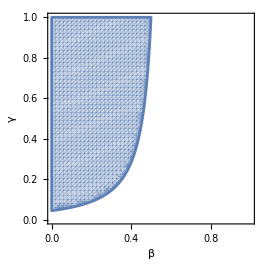

```mathematica
ThresholdPlot[0.05,0.5]
```

We can vary the values of the significance level α and the probability threshold t, to see they alter the “t-probable replication” region.

```mathematica
Manipulate[ThresholdPlot[α,t],{{α,0.01},0,1,Appearance->"Labeled"},{{t,0.5},0.5,1,Appearance->"Labeled"}]
```

Here is a closed-form solution for the “t-probable replication” region.

```mathematica
tRegion[α_,β_,γ_,t_]=FullSimplify[Reduce[Subscript[p, ra][α,β,γ]>t&&0<α<1&&0<β<1&&0<γ<1&&1/2<t<1],0<α<1&&0<β<1&&0<γ<1&&1/2<t<1]
```

t+β<1&&((2 t-α) α)/(-α^2+2 (-1+β)^2+2 t (-1+α+β))<γ

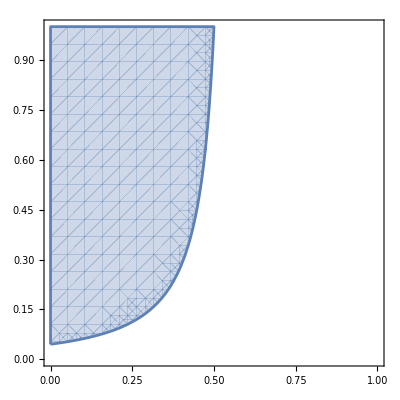

```mathematica
RegionPlot[tRegion[0.05,β,γ,0.5],{β,0,1},{γ,0,1}]
```